# Harper — EIWL Sections 33, 34

## Section 33

```mathematica
Head[ListPlot[{3,5}]]
```

Graphics

```mathematica
Times@@Range[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
f@@@Tuples[{a,b},2]
```

{f[a,a],f[a,b],f[b,a],f[b,b]}

```mathematica
ExpressionTree/@NestList[#^#&,x,4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Cases[Flatten[Table[i^2/(j^2+1),{i,20},{j,20}]],_Integer]
```

{2,8,5,18,32,50,20,10,2,72,98,45,128,17,162,200,80,40,8}

```mathematica
Graph[Rule@@@Partition[Table[Mod[n^2+n,100],{n,100}],2,1]]
```

-Graphics-

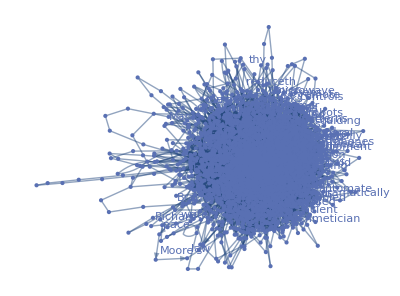

```mathematica
Graph[Rule@@@Partition[TextWords[WikipediaData["Computers"]],2,1],VertexLabels->All]
```

```mathematica
f@@@{{1,2},{7,2},{5,4}}
```

{f[1,2],f[7,2],f[5,4]}

## Section 34

```mathematica
Values[KeySort[Counts[IntegerDigits[3^100]]]]
```

{7,9,9,5,1,5,4,7,1}

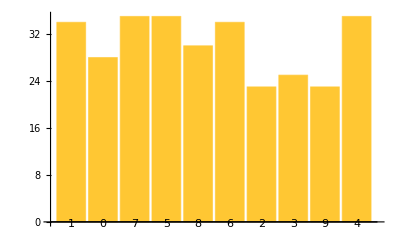

```mathematica
BarChart[Counts[IntegerDigits[2^1000]],ChartLabels->Automatic]
```

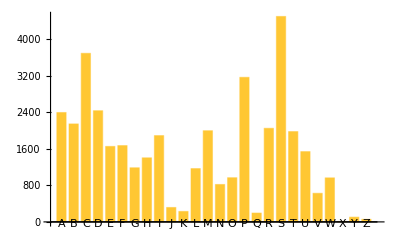

```mathematica
BarChart[Counts[ToUpperCase[StringTake[WordList[],1]]],ChartLabels->Automatic]
```

```mathematica
Take[Sort[Counts[ToUpperCase[StringTake[WordList[],1]]]],-5]
```

<|A→2397,D→2436,P→3168,C→3694,S→4502|>

```mathematica
#q/#u&@LetterCounts[WikipediaData["computers"]]//N
```

0.0401274

```mathematica
TakeLargest[Counts[TextWords[ExampleData[{"Text","AliceInWonderland"}]]],10]
```

<|the→573,and→319,a→269,to→248,she→203,of→194,was→166,Alice→161,in→155,it→154|>